```mathematica
a=10;
r = 10;
sol=NDSolveValue[{n'[t]==-a  n[t] s[t],s'[t]==r (1 - s[t]) - a n[t] s[t],m'[t]==a n[t] s[t],n[0]==10, s[0]== 1, m[0] == 0},{n,s,m},{t,0,1} ]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
sol[[1]][1]
```

1.37334

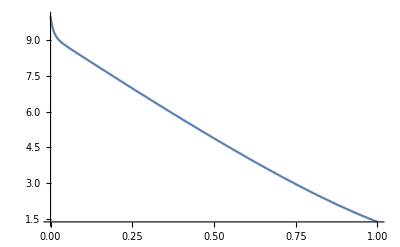

```mathematica
Plot[sol[[1]][t],{t,0,1},PlotRange->Full]
```

```mathematica
calculateFunctionalResponse[n0_,a_,r_]:=Block[{sol},sol=NDSolveValue[{n'[t]==-a  n[t] s[t],s'[t]==r (1 - s[t]) - a n[t] s[t],m'[t]==a n[t] s[t],n[0]==n0, s[0]== 1, m[0] == 0},{n,s,m},{t,0,1} ];n0-sol[[1]][1]]
```

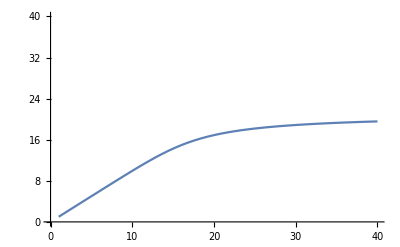

```mathematica
Plot[calculateFunctionalResponse[n0,10,20],{n0,1,40},PlotRange->{Automatic,{0,40}}]
```

```mathematica
(*Parameters*)a=10;(*attack rate*)r=20.0;(*recovery rate*)P=1;(*total number of predators*)(*Initial conditions*)n0=10;(*initial prey*)s0=P;(*all predators start searching*)var0=0;(*assume no initial variance*)(*System of ODEs under naive moment closure*)eqns={n'[t]==-a n[t] s[t],s'[t]==r (P-s[t])-a n[t] s[t],varN'[t]==-2 a s[t] (varN[t]+n[t]^2)+a n[t] s[t]+2 a n[t]^2 s[t]};

(*Initial conditions*)
init={n[0]==n0,s[0]==s0,varN[0]==var0};

(*Solve numerically*)
sol=NDSolve[Join[eqns,init],{n,s,varN},{t,0,1}];
```

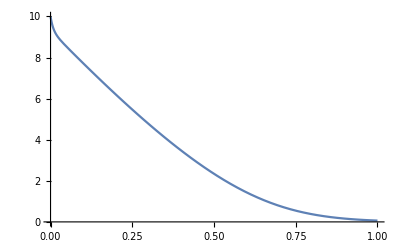

```mathematica
meanN[t_]:=n[t]/. sol;
sdN[t_]:=Sqrt[varN[t]/. sol];

(*Plot with ribbon*)
Plot[{meanN[t]},{t,0,1}]
```

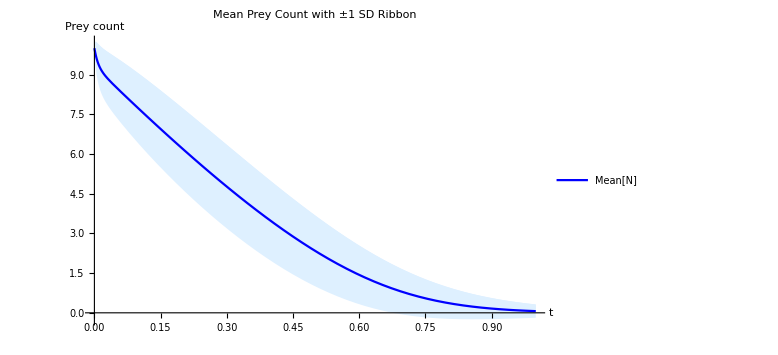

```mathematica
upper[t_]:=meanN[t]+sdN[t];
lower[t_]:=meanN[t]-sdN[t];

(*Plot with ribbon*)
Plot[{meanN[t],upper[t],lower[t]},{t,0,1},PlotStyle->{Blue,None,None},Filling->{1->{2},2->{3}},FillingStyle->LightBlue,PlotLegends->{"Mean[N]"},AxesLabel->{"t","Prey count"},PlotLabel->"Mean Prey Count with ±1 SD Ribbon",ImageSize->Large]
```

```mathematica
upperLowerMeanSolver[n0_,a_,r_]:=Block[{eqns,varN,sol,meanN,sdN},eqns={n'[t]==-a n[t] s[t],s'[t]==r (P-s[t])-a n[t] s[t],varN'[t]==-2 a s[t] (varN[t]+n[t]^2)+a n[t] s[t]+2 a n[t]^2 s[t]};

(*Initial conditions*)
init={n[0]==n0,s[0]==s0,varN[0]==var0};

(*Solve numerically*)
sol=NDSolve[Join[eqns,init],{n,s,varN},{t,0,1}];

meanN[t_]:=n[t]/. sol;sdN[t_]:=Sqrt[varN[t]/. sol];

Flatten@{n0-meanN[1]+sdN[1],n0-meanN[1]-sdN[1],n0-meanN[1]}]
```

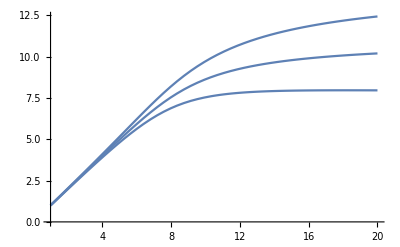

```mathematica
Plot[upperLowerMeanSolver[n0,10,10],{n0,1,20}]
```

```mathematica
PDF[BetaBinomialDistribution[k p,k (1 - p),n],x]
```

Piecewise[{{(Binomial[n,x] Pochhammer[k (1-p),n-x] Pochhammer[k p,x])/Pochhammer[k (1-p)+k p,n], 0≤x≤n}, {0, True}}]

```mathematica
Mean[BetaBinomialDistribution[k p,k (1 - p),n]]
```

(k n p)/(k (1-p)+k p)

```mathematica
Simplify[(k n p)/(k (1-p)+k p)]
```

n p

```mathematica
Variance[BetaBinomialDistribution[k p,k (1 - p),n]]
```

(k^2 n (1-p) p (n+k (1-p)+k p))/((k (1-p)+k p)^2 (1+k (1-p)+k p))

```mathematica
Simplify[(k^2 n (1-p) p (n+k (1-p)+k p))/((k (1-p)+k p)^2 (1+k (1-p)+k p))]
```

-(n (k+n) (-1+p) p)/(1+k)

## True model

```mathematica
upperLowerMeanNumberEaten[N0_,a_,r_,tval_]:=Module[{vars,eqns,init,sol,meanExpr,N2Expr,sdExpr},(*Define state variables*)vars=Flatten[Table[{P[N,1][t],P[N,0][t]},{N,0,N0}]];
(*ODE system with corrected transitions*)eqns=Flatten[Table[{P[N,1]'[t]==-a*N*P[N,1][t]+r*P[N,0][t],P[N,0]'[t]==If[N+1<=N0,a*(N+1)*P[N+1,1][t],0]-r*P[N,0][t]},{N,0,N0}]];
(*Initial conditions*)init=Flatten[Table[{If[N==N0,P[N,0][0]==1,P[N,0][0]==0],P[N,1][0]==0},{N,0,N0}]];
(*Solve the ODEs numerically*)sol=NDSolveValue[Join[eqns,init],Table[{P[N,1][t],P[N,0][t]},{N,0,N0}],{t,0,tval}];
(*Compute mean at time tval using evaluated solution*)meanExpr=Sum[N*(sol[[N+1,1]]+sol[[N+1,2]]/. t->tval),{N,0,N0}];
N2Expr=Sum[N^2*(sol[[N+1,1]]+sol[[N+1,2]]/. t->tval),{N,0,N0}];
sdExpr=Sqrt[N2Expr-meanExpr^2];
{N0-meanExpr+sdExpr,N0-meanExpr-sdExpr,N0-meanExpr}]
```

```mathematica
upperLowerMeanNumberEaten[10,10,10,1]
```

{9.59582,6.09586,7.84584}

```mathematica
meanN[t_]:=n[t]/. sol;
sdN[t_]:=Sqrt[varN[t]/. sol];
```